```mathematica
$Assumptions=y≥1&&μ≥1&&μ∈Reals&&λ>0&&λ∈Reals
```

y≥1&&μ≥1&&μ∈Reals&&λ>0&&λ∈Reals

```mathematica
Reduce[μ==λ/(1-ⅇ^-λ),λ]
```

C[1]∈Integers&&-1+ⅇ^λ≠0&&μ≠0&&λ==μ+ProductLog[C[1],-ⅇ^-μ μ]

```mathematica
Reduce[1==λ/(1-ⅇ^-λ),λ]
```

C[1]∈Integers&&-1+ⅇ^λ≠0&&λ==1+ProductLog[C[1],-1/ⅇ]

```mathematica
λfn[μ_]:=μ+ProductLog[-ⅇ^-μ μ]
L[y_,μ_]:=λfn[μ]^y/(y!(ⅇ^λfn[μ]-1));
l[y_,μ_]:=Log[L[y,μ]]
```

```mathematica
FullSimplify[L[y,y]]
```

-(ProductLog[-ⅇ^-y y] (y+ProductLog[-ⅇ^-y y])^(-1+y))/Gamma[1+y]

```mathematica
FullSimplify[l[y,y]]
```

Log[-(ProductLog[-ⅇ^-y y] (y+ProductLog[-ⅇ^-y y])^(-1+y))/Gamma[1+y]]

```mathematica
Limit[λ/(1-ⅇ^-λ),λ->0]
```

1

```mathematica
Limit[l[y,y],y->1]
```

0

```mathematica
Limit[l[y,μ],μ->1]
```

-∞

```mathematica
Limit[l[2,μ],μ->1]
```

-∞

```mathematica
Limit[l[1,μ],μ->1]
```

0

```mathematica
FullSimplify[l[1,μ]]
```

Log[-ProductLog[-ⅇ^-μ μ]]

```mathematica
dev[y_,μ_]=FullSimplify[l[y,y]-l[y,μ],Assumptions->$Assumptions]
```

Log[-ProductLog[-ⅇ^-y y] (y+ProductLog[-ⅇ^-y y])^(-1+y)]-Log[-ProductLog[-ⅇ^-μ μ] (μ+ProductLog[-ⅇ^-μ μ])^(-1+y)]

```mathematica
Limit[dev[y,μ],μ->1]
```

∞

```mathematica
l[y,y]
```

Log[((y+ProductLog[-ⅇ^-y y])^y)/((-1+ⅇ^(y+ProductLog[-ⅇ^-y y])) y!)]

```mathematica
λofη[η_]:=ⅇ^η
b[η_]=Log[ⅇ^λofη[η]-1]
```

Log[-1+ⅇ^(ⅇ^η)]

```mathematica
ginv[η_]=D[b[η],η]
```

(ⅇ^(ⅇ^η+η))/(-1+ⅇ^(ⅇ^η))

```mathematica
dμdη[η_]=FullSimplify[D[ginv[η],η]]
```

(ⅇ^(ⅇ^η+η) (-1+ⅇ^(ⅇ^η)-ⅇ^η))/((-1+ⅇ^(ⅇ^η))^2)

```mathematica
verify=FullSimplify[dμdη[η]==λofη[η]/(1-ⅇ^(-λofη[η]))(1-λofη[η]/(1-ⅇ^(-λofη[η]))ⅇ^(-λofη[η]))]
```

True

```mathematica
FullSimplify[D[b[η],η]==λofη[η]/(1-ⅇ^(-λofη[η]))]
```

True

```mathematica
V[η_]=FullSimplify[D[b[η],{η,2}]]
```

(ⅇ^(ⅇ^η+η) (-1+ⅇ^(ⅇ^η)-ⅇ^η))/((-1+ⅇ^(ⅇ^η))^2)

```mathematica
V[η]==
```

```mathematica
g[μ_]=Log[λfn[μ]]
```

Log[μ+ProductLog[-ⅇ^-μ μ]]

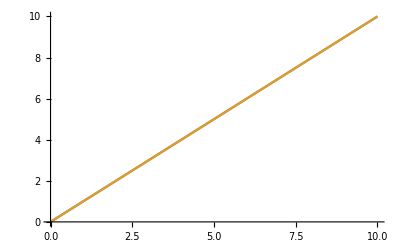

```mathematica
Plot[{g[ginv[η]],η},{η,0,10}]
```

```mathematica
λfn[1]
```

0

```mathematica
1+ProductLog[-ⅇ^-1]
```

0